```mathematica
Table[
With[{g=EdgeDelete[CompleteGraph[8],e]},
{ChromaticPolynomial[g,4]/24,EdgeCount[g]}
]
,{e,Subsets[Map[UndirectedEdge[#[[1]],#[[2]]]&,Subsets[Range[6],{2}]]]}]//Tally//Sort
```

{{{0,16},20},{{0,17},240},{{0,18},1302},{{0,19},3805},{{0,20},5955},{{0,21},6330},{{0,22},4995},{{0,23},3003},{{0,24},1365},{{0,25},455},{{0,26},105},{{0,27},15},{{0,28},1},{{1,18},1296},{{1,19},1140},{{1,20},480},{{1,21},105},{{1,22},10},{{2,17},1080},{{2,18},405},{{2,19},60},{{4,16},435},{{4,17},45},{{8,15},105},{{16,14},15},{{32,13},1}}

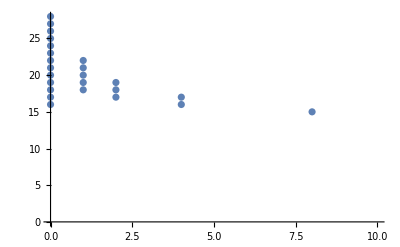

```mathematica
Map[First,Out[41]]//ListPlot
```

```mathematica
Map[Last,Out[6]]//Total
```

32768

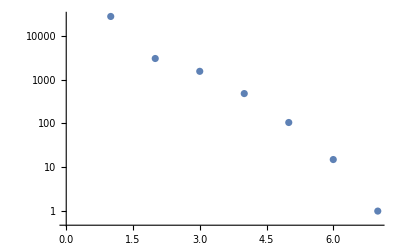

```mathematica
Map[Last,Out[6]]//ListLogPlot
```

```mathematica
Map[First,Map[FactorInteger,Map[Last,Out[6]]]]
```

{{3,1},{7,1},{3,1},{2,5},{3,1},{3,1},{1,1}}

```mathematica
Map[FactorInteger,Map[Last,Out[6]]]
```

{{{3,1},{17,1},{541,1}},{{7,1},{433,1}},{{3,1},{5,1},{103,1}},{{2,5},{3,1},{5,1}},{{3,1},{5,1},{7,1}},{{3,1},{5,1}},{{1,1}}}

```mathematica
Map[Map[First,FactorInteger[#]]&,Map[Last,Out[6]]]
```

{{3,17,541},{7,433},{3,5,103},{2,3,5},{3,5,7},{3,5},{1}}

```mathematica
Map[Map[First,FactorInteger[#]]&,Map[Last,Out[6]]]
```

{{3,17,541},{7,433},{3,5,103},{2,3,5},{3,5,7},{3,5},{1}}

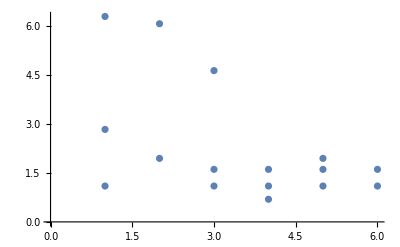

```mathematica
ListPlot[Flatten[
With[{list=Map[Map[First,FactorInteger[#]]&,Map[Last,Out[6]]]},
Table[Map[{k,Log[#]}&,list[[k]]],{k,1,6}]
],1]]
```

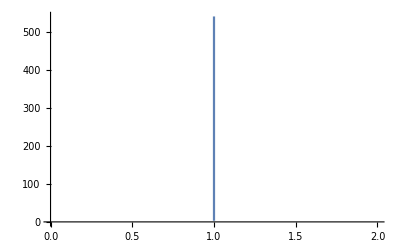
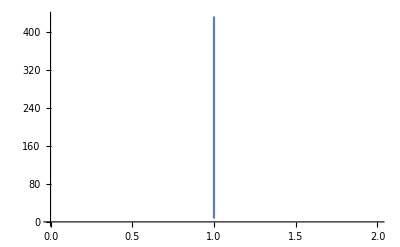
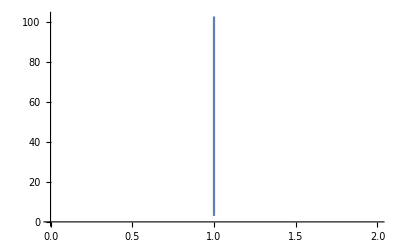
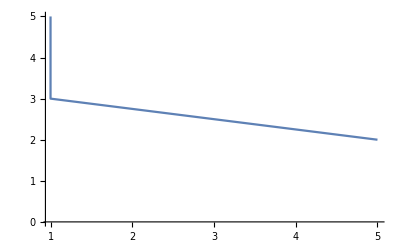
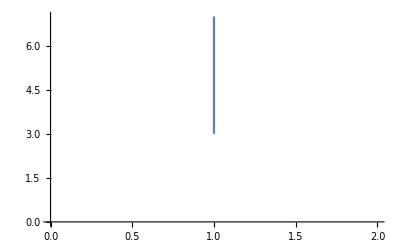
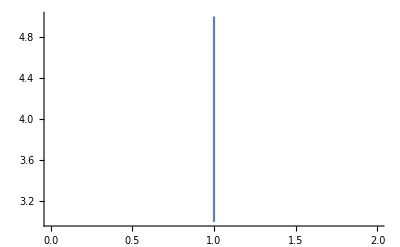
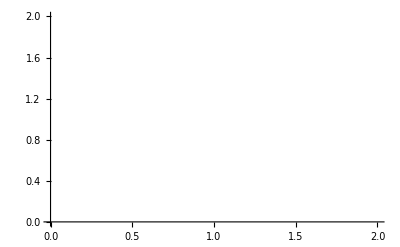

```mathematica
Map[ListLinePlot,Map[Map[Reverse,FactorInteger [#]]&,Map[Last,Out[6]]]]
```

## More nodes

```mathematica
Subsets[Map[UndirectedEdge[#[[1]],#[[2]]]&,Subsets[Range[8],{2}]]]
```

$Aborted

```mathematica
MemoryInUse[]
```

130739928

```mathematica
Monitor[Sort[Tally[Table[
With[{g=EdgeDelete[CompleteGraph[7],e]},
{ChromaticPolynomial[g,4]/24,EdgeCount[g]}
]
,{e,Subsets[Map[UndirectedEdge[#[[1]],#[[2]]]&,Subsets[Range[7],{2}]]]}]]],e]
```

{{{0,10},21},{{0,11},231},{{0,12},1155},{{0,13},3465},{{0,14},6825},{{0,15},9037},{{0,16},8169},{{0,17},4200},{{0,18},1225},{{0,19},210},{{0,20},21},{{0,21},1},{{1,15},8435},{{1,16},6300},{{1,17},1470},{{1,18},105},{{2,14},21210},{{2,15},18375},{{2,16},4515},{{2,17},315},{{3,13},8400},{{3,14},19950},{{3,15},8330},{{3,16},1260},{{4,12},1400},{{4,13},31500},{{4,14},26460},{{4,15},8085},{{5,13},12600},{{5,14},16380},{{5,15},252},{{6,12},26110},{{6,13},44940},{{6,14},11550},{{6,16},105},{{7,12},3780},{{7,13},20160},{{7,14},360},{{7,15},1750},{{8,11},4095},{{8,12},32130},{{8,13},18270},{{8,14},7560},{{9,11},7350},{{9,12},25200},{{9,13},10290},{{9,14},5145},{{10,12},34650},{{10,13},26040},{{11,12},6300},{{11,13},11340},{{11,14},315},{{12,10},2310},{{12,11},44730},{{12,12},44100},{{12,13},3150},{{12,14},525},{{13,11},2520},{{13,12},14700},{{13,13},6300},{{14,11},13860},{{14,12},25200},{{14,13},6090},{{15,11},18144},{{15,12},25200},{{16,9},210},{{16,10},6300},{{16,11},31731},{{16,12},22155},{{17,11},3780},{{17,12},7560},{{17,13},735},{{18,10},24990},{{18,11},54495},{{18,12},10500},{{19,11},3780},{{19,12},6300},{{20,10},4284},{{20,11},55230},{{20,12},2520},{{21,10},7980},{{21,11},25200},{{21,12},630},{{21,13},210},{{22,11},13860},{{22,12},1785},{{23,11},10080},{{23,12},1260},{{24,9},7385},{{24,10},65940},{{24,11},32130},{{25,11},5040},{{26,10},10080},{{26,11},8190},{{26,12},1260},{{27,9},6860},{{27,10},28665},{{27,11},5040},{{28,9},1260},{{28,10},44520},{{28,11},1260},{{29,10},1260},{{29,11},5040},{{30,10},61110},{{30,11},1260},{{31,10},1260},{{31,11},3150},{{32,8},630},{{32,9},8505},{{32,10},22995},{{32,11},1260},{{33,10},8820},{{34,10},12600},{{35,10},8820},{{35,11},840},{{36,8},3045},{{36,9},75810},{{36,10},18060},{{37,10},2520},{{38,10},2520},{{77/2,12},35},{{39,9},7560},{{39,10},8820},{{40,9},20160},{{41,9},1260},{{41,10},5040},{{42,9},69300},{{43,10},840},{{87/2,11},420},{{44,9},1260},{{44,10},630},{{45,9},22050},{{46,9},8820},{{47,9},5040},{{48,7},525},{{48,8},19215},{{48,9},17640},{{49,9},11340},{{99/2,10},1260},{{51,9},16170},{{103/2,10},630},{{52,8},1260},{{52,9},1260},{{105/2,10},420},{{53,9},2520},{{54,8},56595},{{55,9},420},{{56,8},10080},{{56,9},1260},{{113/2,10},21},{{115/2,9},840},{{119/2,9},2520},{{60,8},23310},{{61,8},2520},{{123/2,9},3780},{{63,8},52920},{{64,6},35},{{64,7},1470},{{64,8},2520},{{129/2,9},630},{{67,8},1260},{{68,8},2520},{{69,8},7560},{{70,8},2520},{{70,9},70},{{143/2,8},1260},{{72,7},22785},{{147/2,8},8190},{{153/2,8},7350},{{80,7},3150},{{81,7},36015},{{82,8},630},{{84,7},15225},{{86,8},105},{{90,7},8820},{{91,7},360},{{183/2,7},2520},{{92,7},1260},{{189/2,7},20580},{{96,6},3535},{{98,7},1260},{{102,7},2310},{{108,6},20090},{{112,6},1260},{{120,6},2772},{{243/2,6},16807},{{122,6},420},{{126,6},9135},{{128,5},210},{{136,6},210},{{144,5},4935},{{160,5},252},{{162,5},13377},{{168,5},1575},{{192,4},630},{{216,4},5250},{{224,4},105},{{256,3},35},{{288,3},1295},{{384,2},210},{{512,1},21},{{2048/3,0},1}}

```mathematica
TableForm[Table[Select[Map[First,Out[1]],#[[1]]==k&]//Sort,{k,0,512}],TableDepth->1]
```

{{0,10},{0,11},{0,12},{0,13},{0,14},{0,15},{0,16},{0,17},{0,18},{0,19},{0,20},{0,21}}
{{1,15},{1,16},{1,17},{1,18}}
{{2,14},{2,15},{2,16},{2,17}}
{{3,13},{3,14},{3,15},{3,16}}
{{4,12},{4,13},{4,14},{4,15}}
{{5,13},{5,14},{5,15}}
{{6,12},{6,13},{6,14},{6,16}}
{{7,12},{7,13},{7,14},{7,15}}
{{8,11},{8,12},{8,13},{8,14}}
{{9,11},{9,12},{9,13},{9,14}}
{{10,12},{10,13}}
{{11,12},{11,13},{11,14}}
{{12,10},{12,11},{12,12},{12,13},{12,14}}
{{13,11},{13,12},{13,13}}
{{14,11},{14,12},{14,13}}
{{15,11},{15,12}}
{{16,9},{16,10},{16,11},{16,12}}
{{17,11},{17,12},{17,13}}
{{18,10},{18,11},{18,12}}
{{19,11},{19,12}}
{{20,10},{20,11},{20,12}}
{{21,10},{21,11},{21,12},{21,13}}
{{22,11},{22,12}}
{{23,11},{23,12}}
{{24,9},{24,10},{24,11}}
{{25,11}}
{{26,10},{26,11},{26,12}}
{{27,9},{27,10},{27,11}}
{{28,9},{28,10},{28,11}}
{{29,10},{29,11}}
{{30,10},{30,11}}
{{31,10},{31,11}}
{{32,8},{32,9},{32,10},{32,11}}
{{33,10}}
{{34,10}}
{{35,10},{35,11}}
{{36,8},{36,9},{36,10}}
{{37,10}}
{{38,10}}
{{39,9},{39,10}}
{{40,9}}
{{41,9},{41,10}}
{{42,9}}
{{43,10}}
{{44,9},{44,10}}
{{45,9}}
{{46,9}}
{{47,9}}
{{48,7},{48,8},{48,9}}
{{49,9}}
{}
{{51,9}}
{{52,8},{52,9}}
{{53,9}}
{{54,8}}
{{55,9}}
{{56,8},{56,9}}
{}
{}
{}
{{60,8}}
{{61,8}}
{}
{{63,8}}
{{64,6},{64,7},{64,8}}
{}
{}
{{67,8}}
{{68,8}}
{{69,8}}
{{70,8},{70,9}}
{}
{{72,7}}
{}
{}
{}
{}
{}
{}
{}
{{80,7}}
{{81,7}}
{{82,8}}
{}
{{84,7}}
{}
{{86,8}}
{}
{}
{}
{{90,7}}
{{91,7}}
{{92,7}}
{}
{}
{}
{{96,6}}
{}
{{98,7}}
{}
{}
{}
{{102,7}}
{}
{}
{}
{}
{}
{{108,6}}
{}
{}
{}
{{112,6}}
{}
{}
{}
{}
{}
{}
{}
{{120,6}}
{}
{{122,6}}
{}
{}
{}
{{126,6}}
{}
{{128,5}}
{}
{}
{}
{}
{}
{}
{}
{{136,6}}
{}
{}
{}
{}
{}
{}
{}
{{144,5}}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{{160,5}}
{}
{{162,5}}
{}
{}
{}
{}
{}
{{168,5}}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{{192,4}}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{{216,4}}
{}
{}
{}
{}
{}
{}
{}
{{224,4}}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{{256,3}}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{{288,3}}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{{384,2}}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{{512,1}}